```mathematica
Generator[length_,size_]:=Table[Total[If[#1<#2,0,1]&@@@Subsets[RandomSample[Range[length]],{2}]],size];
```

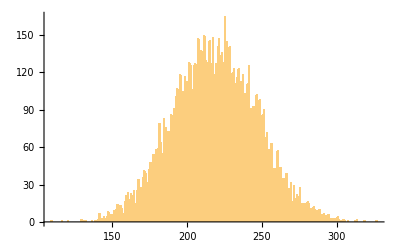

```mathematica
Histogram[Generator[30,10000],{1}]
```

```mathematica
FindDistribution[Generator[30,10000],3]
```

{PascalDistribution[43,0.197994],MixtureDistribution[{0.489121,0.510879},{PoissonDistribution[194.426],PoissonDistribution[238.963]}],MixtureDistribution[{0.363733,0.636267},{DiscreteUniformDistribution[{119,216}],PoissonDistribution[233.387]}]}

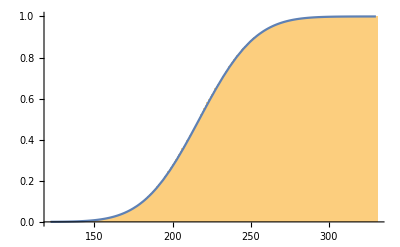

```mathematica
Show[Histogram[#,{1},"CDF"],Plot[CDF[NormalDistribution[Mean[#],StandardDeviation[#]],x],{x,Min[#],Max[#]}]]&[Generator[30,10000]]
```

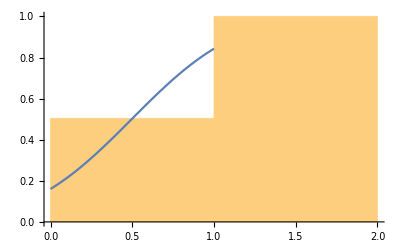
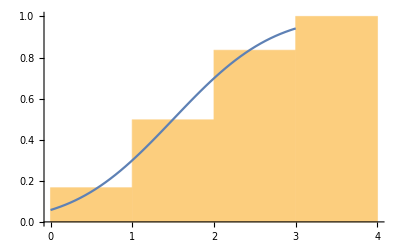
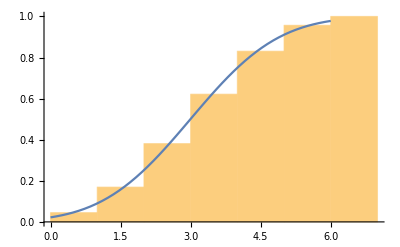
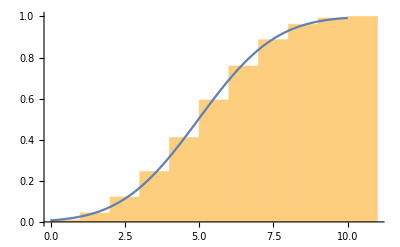
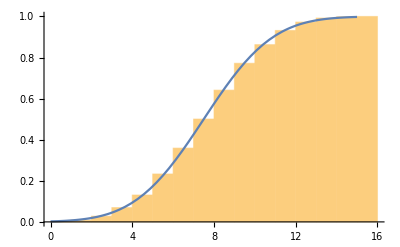
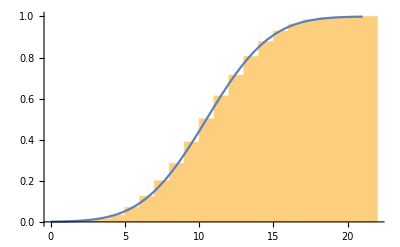
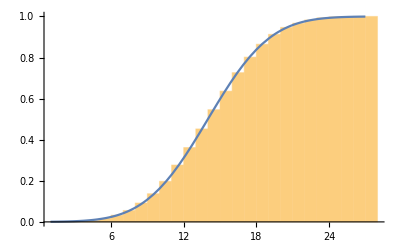
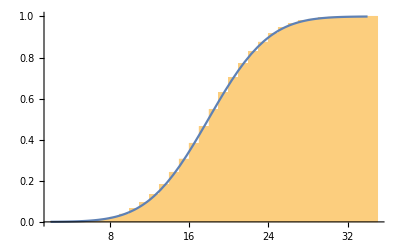

```mathematica
Table[Show[Histogram[#,{1},"CDF"],Plot[CDF[NormalDistribution[Mean[#],StandardDeviation[#]],x],{x,Min[#],Max[#]}]]&[Generator[i,10000]],{i,2,30}]
```